```mathematica
SOI=Import["/users/pp/Desktop/soi.txt", "table"];
TSID=Import["/users/pp/Desktop/tsi.txt", "table"];
QBO=Import["/users/pp/Desktop/qbo20.txt", "table"];
QBO70=Import["/users/pp/Desktop/qbo.txt", "table"];
CW=Import["/users/pp/Desktop/cw.txt", "table"];
CW1=Import["/users/pp/Desktop/cw1_1930.txt", "table"];
CW0=Import["/users/pp/Desktop/cw1.txt", "table"];
NINO34=Import["/users/pp/Desktop/nino34ke.txt", "table"];
tahiti=Import["/users/pp/Desktop/tahiti.txt", "table"];
darwin=Import["/users/pp/Desktop/darwin0.txt", "table"];
```

```mathematica
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 212;    WinHiFilter = 9;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=24; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.034*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
```

80.0069

{0.,-44.1774}

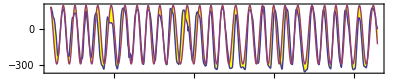

```mathematica
qbo[x_] :=  Cos[2.6956*(x+0.24*Sin[0.523*x+2.82]-0.07*Sin[0.12*x+0.2])+1.44] ; 
QBOM = Table[{1953.0+x, -240*qbo[73.0+x]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

80.1

2.33056

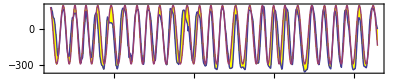

```mathematica
QB=2.696; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.523*x+2.82]-0.07*Sin[0.12*x+0.2])+1.44] ; 
QBOM = Table[{1953.0+x, -240*qbo[73.0+x]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM];
2*Pi/QB
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

70.2574

6.47885

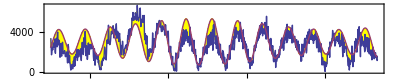

```mathematica
(* Variance[CW1]-Variance[CWM] *)

CW =0.9698; cw[x_] := Sin[CW*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
CWT = MeanFilter[CW1[[All,2]],3];
CWM = Table[{1880+i, 1770*cw[i-1.3]+3000},{i,50,133+2/12, 1/12}];
100*Correlation[CW1,CWM][[2,2]]
2*Pi/CW
ListLinePlot[{CW1,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

75.4216

6.47885

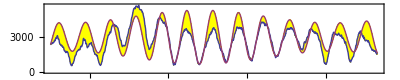

```mathematica
(* Variance[CW1]-Variance[CWM] *)

CWF =0.9698; cw[x_] := Sin[CWF*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
CWD = MeanFilter[CW1[[All,2]],5];
CWM = Table[{1880+i, 1770*cw[i-1.42]+3000},{i,50+1/12,133-0/12, 1/12}];
CWT = Table[{1880+50+i/12, CWD[[i]]},{i,1,(83+0/12)*12, 1}];
100*Correlation[CWT,CWM][[2,2]] 
2*Pi/CWF
ListLinePlot[{CWT,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

91.5396

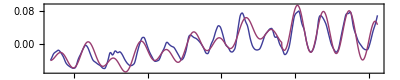

```mathematica
(* Number 1 *)
HALE:=0.5875; HALE2:=0.596;
tsi[x_] := +1.12*If[x<95.0,
                    0.8*(1.58*Cos[HALE*(x-0.029)] + 1.3*Cos[HALE/2*(x-6.7)]+0.22*Cos[HALE/3*(x+3.3)]),
                    1.0*(3.1*Cos[HALE2*(x-1.28)]+0.35*Cos[HALE/2*(x-3.92)]) ] +
                    2.4*Cos[2*Pi*x/153.0-1] ; 
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 0*MeanFilter[TSID[[All,2]],200]; 
TSIT = Table[{1880+i/12, 2.75*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -0.015*(tsi[x+0.39])},{x,STRT/12,LNGTH/12, 1/12}];
100*Correlation[TSIT,TSIM][[2,2]]
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"TSI", "Model"}]
```

92.318

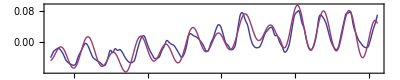

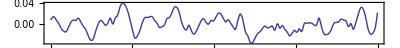

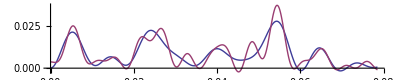

```mathematica
(* Number 2 *)
sigmoid[x_] := 1/(1+Exp[3.2*(x-94.1)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.8*(2.2*Cos[HALE*(x-0.029)] + 1.3*Cos[HALE/2*(x-6.7)]+0.22*Cos[HALE/3*(x+3.3)]) +
                   (1-sigmoid[x])*1.0*(3.1*Cos[HALE2*(x-1.28)]+0.35*Cos[HALE/2*(x-3.92)])) +  
             2.4*Cos[2*Pi*x/153.0-1]; 
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 0*MeanFilter[TSID[[All,2]],200]; 
TSIT = Table[{1880+i/12, 2.75*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -0.015*(tsi[x+0.39])},{x,STRT/12,LNGTH/12, 1/12}];
100*Correlation[TSIT,TSIM][[2,2]]
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"TSI", "Model"}] 
SDIF = TSIT[[All,2]]-TSIM[[All,2]];  
ListLinePlot[SDIF, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/40},PlotRange->All,AspectRatio->0.2]
```

96.4942   0.

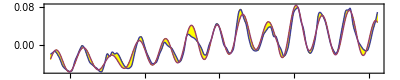

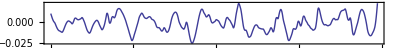

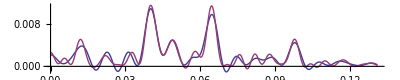

```mathematica
(* Number 3 *)
sigmoid[x_] := 1/(1+Exp[6*(x-94.0)]); 
HALE:=0.59; HALE2:=0.596;
tsi[x_] := +1.12*((sigmoid[x])*0.62*(2.7*Cos[HALE*(x-0.11)] + 0.7*Cos[HALE/2*(x-5.7)]+0.18*Cos[HALE/3*(x+3.8)]) +
                   (1-sigmoid[x])*0.99*(3.12*Cos[HALE2*(x-1.29)]+0.55*Cos[HALE/2*(x-7.0)])) +  
             2.42*Cos[2*Pi*x/153.1-1.0] +0.62*Cos[2*Pi*x/9.57+1.5] + 0.55*Cos[2*Pi*x/105.0+0.4] + 0*0.39*Cos[2*Pi*x/12.9+2.5]; 
TSDATA= 1*MeanFilter[TSID[[All,2]],0] - 0*MeanFilter[TSID[[All,2]],200]; 
TSIT = Table[{1880+i/12, 2.75*TSDATA[[i]]},{i,STRT,LNGTH,1}]; 
TSIM = Table[{1880.0+x, -0.015*(tsi[x+0.39])},{x,STRT/12,LNGTH/12, 1/12}];
OldCC = NewCC; NewCC = 100*Correlation[TSIT,TSIM][[2,2]]; Print[NewCC, "   ", NewCC-OldCC];
ListLinePlot[{TSIT, TSIM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"TSI", "Model"}] 
SDIF = TSIT[[All,2]]-TSIM[[All,2]];  
ListLinePlot[SDIF, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/24},PlotRange->All,AspectRatio->0.2]
```

{char t,4.24094,-0.00622302, Years from,1880.5,to,2013.58,CC,96.4942,9.68573,-86.8085}

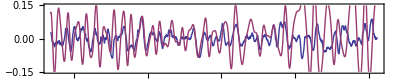

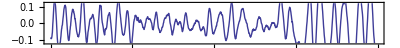

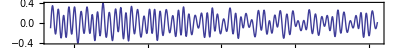

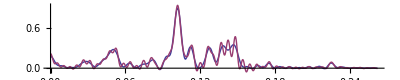

```mathematica
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 220;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.034*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.195;  dilate[x_] := -0*(0.185*Sin[0.07*x+0.9]+0.13*Cos[2*Pi*x+1.5]);  ClSh := 1002.32; (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
RHS[x_] := 0*(-0.2*Cos[4*Pi*x*1-0.009] - 0.2*Cos[2*Pi*x*1.0188-0.1]) + 
          2.8*(0.078*qbo[x+0.7]*(0.99+0.12*tsi[x-0.8])-
          0.026*cw[x+0.05]-0.000*tsi[x+4.1]-0.0055 -0.000002*x );
NDSolve[{y''[x]+(CF+0.35*tsi[x-0.8]-0.18*cw[x+0.6])*y[x] == RHS[x],  y'[52.0]==-0.01, y[52.0]==+0.03}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0*0.03*Cos[2*Pi/4.5*x+1.0]+First[-0.5*y[x+dilate[x]+0.39] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
```

{char t,4.22844,-0.0000186068, Years from,1880.5,to,2013.58,CC,26.7091,61.7584,35.0493}

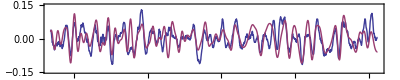

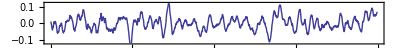

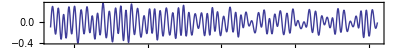

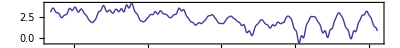

```mathematica
(* NUMBER 1 *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 210;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.045*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.208;  dilate[x_] := -(0.16*Sin[0.074*x+0.7]-0.0*Cos[2*Pi*x+1.5]); (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
Hill[x_] := CF+0.353*tsi[x-0.77]*(1+0.19*qbo[x+0.5])-0.2*cw[x+0.72];
RHS[x_] := 0*0.9*(-0.2*Cos[4*Pi*x*1-0.3] - 0.14*Cos[2*Pi*x-0.3]) + 2.7*(0.077*qbo[x+0.7]*(1+0.13*tsi[x-1.1])-
          0.025*cw[x+0.04]-0.0013*tsi[x+4.2]-0.005 +0.00000*x );
NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x],  y'[52.0]==-0.023, y[52.0]==+0.016}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0.034*Cos[2*Pi/4.518*x+1.6]+0.007*qbo[x+0.03]+ First[-0.49*y[1.0006*x+dilate[x]+0.41] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]  *)
```

{char t,4.51106,-0.0000207042, Years from,1880.5,to,2013.58,CC,37.9264,37.9264,0.}

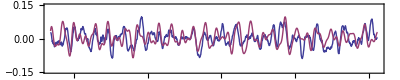

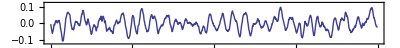

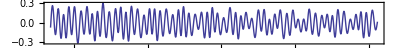

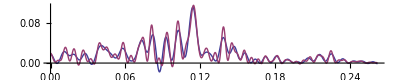

```mathematica
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 220;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.034*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 1.94;  dilate[x_] := -0*(0.185*Sin[0.07*x+0.9]+0.13*Cos[2*Pi*x+1.5]);  ClSh := 1002.32; (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
RHS[x_] := 0*(-0.2*Cos[4*Pi*x*1-0.009] - 0.2*Cos[2*Pi*x*1.0188-0.1]) + 
          2.0*(0.089*qbo[x+0.72]*(0.99+0.1*tsi[x-0.8])-
          0.026*cw[x+0.05]-0.000*tsi[x+4.1]-0.0055 -0.000002*x );
NDSolve[{y''[x]+(CF+0.05*tsi[x+0.2]-0.12*cw[x+0.6])*y[x] == RHS[x],  y'[52.0]==-0.01, y[52.0]==+0.03}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0*0.03*Cos[2*Pi/4.5*x+1.0]+First[-0.5*y[x+dilate[x]+0.5] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
```

{char t,4.23324,0.0000281368, Years from,1880.5,to,2013.58,CC,64.0166,64.0677,0.0511049}

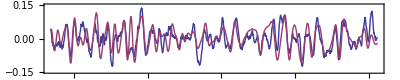

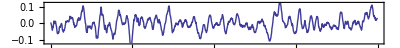

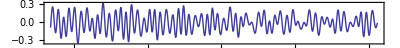

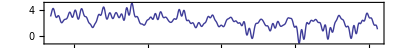

```mathematica
(* NUMBER 2  *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 214;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=6; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.048*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.203;  dilate[x_] := -(0.09*Sin[0.074*x+0.7]-0.0*Cos[2*Pi*x+1.5]); (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
Hill[x_] := CF+0.342*tsi[x-1.19]*(1+0.52*qbo[x+0.458])-0.38*cw[x+0.84];
RHS[x_] := -0*0.9*(-0.1*Cos[4*Pi*x+1.3] - 0.06*Cos[2*Pi*x-1.3]) + 2.75*(0.062*qbo[x+0.69]*(0.99+0.13*tsi[x-1.18])-
          0.026*cw[x+0.04]-0.0011*tsi[x+5.0]-0.0048 +0.00000*x );
NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.02],  y'[52.0]==-0.042, y[52.0]==+0.016}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, -0.03*Cos[2*Pi/4.52*x+1.6]+0.0051*qbo[x+0.03]+ First[-0.52*y[1.0014*x+dilate[x]+0.38] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.15,0.15+SEP},Frame->True,Axes->False,  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.12,0.12}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]  *)
```

{char t,4.23901,0.000945165, Years from,1880.17,to,2013.58,CC,65.3906,65.2623,-0.128313}

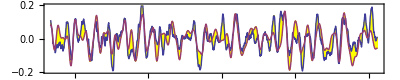

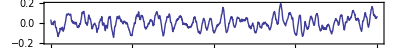

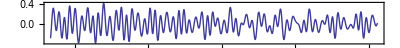

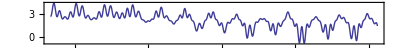

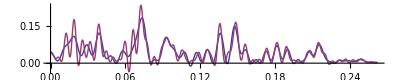

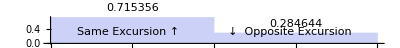

```mathematica
(* NUMBER 3  *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 210;    WinHiFilter = 8;
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter] - 1*MeanFilter[darwin[[All,2]],WinLowFilter]) - (1*MeanFilter[tahiti[[All,2]],WinHiFilter] - 1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.075*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.19*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]); (* + 0*0.008*DiracDelta[x-50.0] 1.98 *)
OSC := 9.0786;     TR =52.01;
Hill[x_] := CF+0.359*tsi[x-1.53]*(1.03+0.62*qbo[x+0.43])-0*0.05*cw[x-2.2] ;
Osc[x_] := 0.042*(Cos[2*Pi/OSC*x+4.35]-Cos[4*Pi/OSC*x+2.14]) +0*0.03*Cos[2*Pi/7.3*x+0.5];
RHS[x_] :=+ 2.99*(0.061*qbo[x+0.72]*(1+0.16*tsi[x+0.64])- 0.032*cw[x+0.05]+0.0004*tsi[x+3.9]+0.0005 +0.000007*x-0*0.01*Osc[x-0.6] );  
NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.07],  y'[TR]==-0.01, y[TR]==+0.0052}, y, {x, 0, 260}];   
SOIM = Table[{1880.0+x, Osc[x]+ 0*0.01*tsi'[x-4.5]+First[-0.49*y[1.0008*x+dilate[x]+0.63] /. %]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.2,0.2+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.2,0.2}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.1] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,0.000118369, Years from,1880.17,to,2013.58,CC,73.8,72.8382,-0.96181}

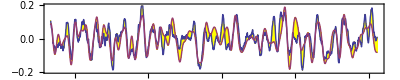

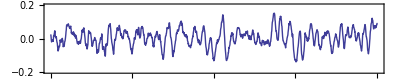

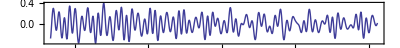

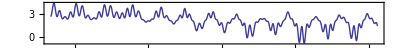

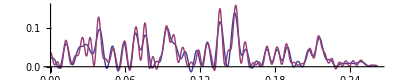

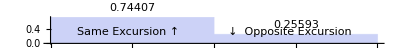

```mathematica
(* NUMBER 3  *)
(* ################################### SIMPLIFIED VERY GOOD ##################################### *)
WinLowFilter = 210;    WinHiFilter = 8;  (* 8 *)
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.073*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.19*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]);
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43])  ;
Osc[x_] := 0.039*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.033*Cos[2*Pi/7.3*x+0.47] - 0.026*Cos[2*Pi*x/27.3-0.6];
RHS[x_] :=+ 2.98*(0.06*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.032*cw[x+0.04]+0.0006*tsi[x+3.9]+0.0008+0.000007*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.01, y[TR]==+0.0052}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]+0.009*tsi'[x-4.4]-0.009*qbo[x-0.6]+First[-0.49*y[1.0008*x+dilate[x]+0.63] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-0.2,0.2+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-0.2,0.2}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.2]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

```mathematica
0.009/0.073
```

0.123288

{char t,4.23901,-0.00930279, Years from,1880.17,to,2013.58,CC,96.4635,73.7697,-22.6939}

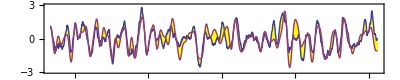

```mathematica
(* NUMBER 3  *)
(* ################################### From data ##################################### *)
WinLowFilter = 214;    WinHiFilter = 11;  (* 8 *)
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -1.1*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -0.18*Sin[0.074*x-0.5];
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]) -  0*0.12*Osc[x-0.9];
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.438*Cos[2*Pi/7.3*x+0.47] - 0.356*Cos[2*Pi*x/(3*OSC)-0.6];
RHS[x_] :=+ 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.011+0.0001*x -0*0.014*tsi'[x+5.6]-0*0.15*qbo'[x]);  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.02, y[TR]==+0.03}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]-0.123*qbo[x-0.6]+First[-0.48*y[1.0004*x+dilate[x]+0.66] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,4.23901,-0.00930279, Years from,1880.17,to,2013.58,CC,96.4942,73.7697,-22.7246}

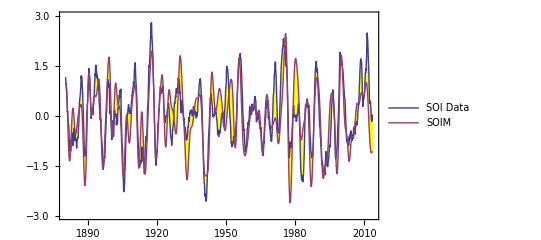

-Graphics-

-Graphics-

```mathematica
WinLowFilter = 214;    WinHiFilter = 11;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
    (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -1.1*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -0.18*Sin[0.074*x-0.5];
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]);
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.438*Cos[2*Pi/7.3*x+0.47];
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.011+0.0001*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*(y[x] +0*0.00015*(y[x])^3) == RHS[x-0.08],  y'[TR]==-0.02, y[TR]==+0.03}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]-0.123*qbo[x-0.6]+First[-0.48*y[1.0004*x+dilate[x]+0.66] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.6] 
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  WaveletScalogram[CWTT]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  WaveletScalogram[CWTM]
```

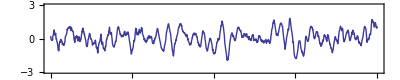

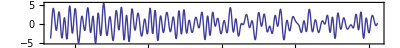

-Graphics-

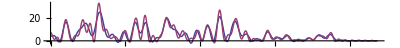

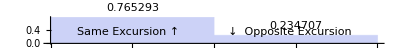

```mathematica
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,-0.221929, Years from,1880.17,to,2013.58,CC,61.9982,62.9162,0.917991}

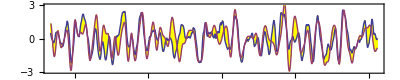

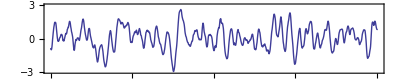

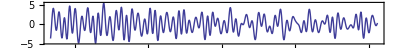

-Graphics-

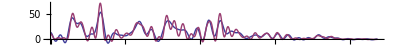

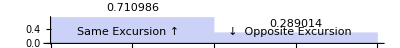

```mathematica
(* NUMBER 3  applied to NINO34 *)
(* ################################### From data ##################################### *)
WinLowFilter = 215;    WinHiFilter = 10;  (* 8 *)
R = 2.2*(MeanFilter[NINO34[[All,2]],WinHiFilter] - MeanFilter[NINO34[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.97*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.2*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]);
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.355*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43])  ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.438*Cos[2*Pi/7.3*x+0.47] - 0.356*Cos[2*Pi*x/27.3-0.6];
RHS[x_] :=+ 2.9*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.01+0.0001*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.07],  y'[TR]==-0.12, y[TR]==+0.04}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]+0.12*tsi'[x-4.4]-0.12*qbo[x-0.6]+First[-0.68*y[1.00091*x+dilate[x]+0.73] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1]
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,0.0215803, Years from,1880.17,to,2013.58,CC,52.8682,52.8899,0.0216449}

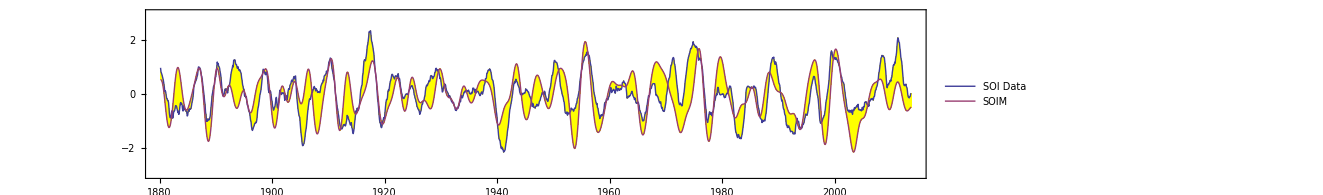

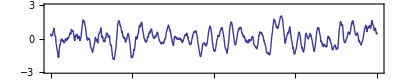

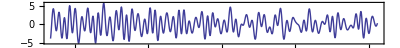

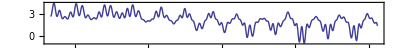

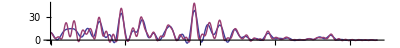

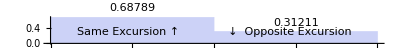

```mathematica
(* NUMBER 3  *)
(* ################################### From data ##################################### *)
WinLowFilter = 214;    WinHiFilter = 11;  (* 8 *)
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; (* 1603 STRT=590;   STRTY=1880+STRT/12; SEP=0.0; LNGTH=1190; ENDY=1880+LNGTH/12; *)
SOIT = Table[{1880+i/12, -0.92*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.197;  dilate[x_] := -(0.19*Sin[0.074*x-0.5]+0.0*Cos[2*Pi*x-0.2]);
OSC := 9.08;     TR=52.01;
Hill[x_] := CF+0.37*tsi[x-1.6]*(1.03+0.61*qbo[x+0.43])  ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) +0.438*Cos[2*Pi/7.3*x+0.47] - 0.356*Cos[2*Pi*x/27.3-0.6];
RHS[x_] :=+ 3.1*(0.82*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]-0.04*tsi'[x+4.7] +0.011+0.0001*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.02, y[TR]==+0.03}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, 0*Osc[x]-0.123*qbo[x-0.6]+First[-0.48*y[1.0009*x+dilate[x]+0.66] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2] 
RHSD = Table[{1880+i/12, RHS[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{RHSD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
HillD = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{HillD}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Hill"}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

```mathematica
WinLowFilter = 214;    WinHiFilter = 12;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
    (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -1.174*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.203;  dilate[x_] := -0.23*Sin[0.074*x-0.5];
OSC := 9.086;     TR=52.0;
Hill[x_] := CF+0.36*tsi[x-1.54]*(1.03+0.61*qbo[x+0.42]);
Osc[x_] := 0.53*(Cos[2*Pi/OSC*x+4.5]-Cos[4*Pi/OSC*x+2.25]) - 0.4*Cos[2*Pi*x/(3*OSC)-0.6] +0.46*Cos[2*Pi/7.3*x+0.47];
RHS[x_] := 2.82*(0.73*qbo[x+0.74]*(0.85+0.16*tsi[x+0.62])-0.47*cw[x+0.04]+0.015*tsi[x+4.6]+0.011+0.00014*x );  
A = 2.844;   QQ = 2.771;  W = 1.021;
mq[x_] := 0*0.58*(0.3*MathieuS[A,QQ,W*x]-0.16*MathieuC[A,QQ,W*x]);
SOLN=NDSolve[{y''[x]-0.063*y'[x]*(1-0.4*y[x]*y[x])+Hill[x]*y[x] == RHS[x-0.07],  y'[TR]==-0.095, y[TR]==+0.15}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]-0.12*qbo[x-0.6]-0*0.22*cw[x/2+1.2]+0.11*tsi'[x-4.8]+First[-0.47*y[1.0007*x+dilate[x]+0.68] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2] 
(*
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
*)
```

{char t,4.2851,-0.149375, Years from,1880.17,to,2013.58,CC,32.9187,32.9187,0.}

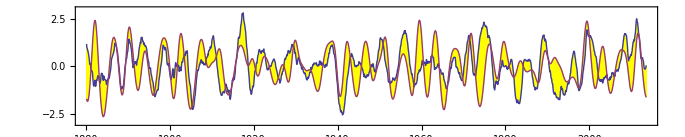

```mathematica
(*intentionally wrong *)
WinLowFilter = 214;    WinHiFilter = 11;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
    (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -1.1*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.15;  dilate[x_] := -0.1*Sin[0.074*x-0.5];
OSC := 9.08;     TR=52.01;
tsi[x_] := Cos[2*Pi*x/10.0+0.2];  qbo[x_] := Cos[2*Pi*x/2.48-2.7];  cw[x_] := Cos[2*x*Pi/6.8+3.1];
Hill[x_] := CF+1*tsi[x-2.5]*(0.95+0.7*qbo[x+0.6]);
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.438*Cos[2*Pi/7.3*x+0.47];
RHS[x_] := 2.9*(0.9*qbo[x+0.4]*(1+0.9*tsi[x+0.3])-0.43*cw[x+0.1]+0.6*tsi[x+4.3]+0.013+0.0001*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x+0.0],  y'[TR]==+0.2, y[TR]==+0.2}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, 0*Osc[x]+0.2*qbo[x-0.6]+First[-0.48*y[1.*x+dilate[x]+0.5] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,4.27517,0.21583, Years from,1880.17,to,2013.58,CC,34.2181,34.2181,0.}

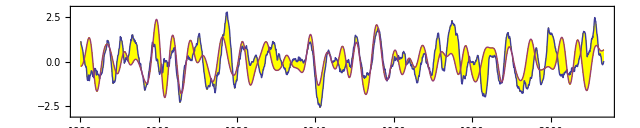

```mathematica
WinLowFilter = 214;    WinHiFilter = 11;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
    (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -1.1*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.16;  dilate[x_] := -0.0*Sin[0.074*x-0.5];
OSC := 9.08;     TR=52.01;
tsi[x_] := Cos[2*Pi*x/9.5-0.9];  qbo[x_] := Cos[2*Pi*x/2.8-3.1];  cw[x_] := Cos[2*x*Pi/5.7+3.8];
Hill[x_] := CF+0.3*tsi[x-2.5]*(2.2+0.4*qbo[x+0.1]);
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.438*Cos[2*Pi/7.3*x+0.47];
RHS[x_] := 2.9*(0.3*qbo[x+0.6]*(1.5+0.6*tsi[x+0.2])-0.5*cw[x+0.2]+0.4*tsi[x+5.2]+0.013+0.0001*x );  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x+0.0],  y'[TR]==-0.3, y[TR]==+0.2}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, 0*Osc[x]+0.2*qbo[x-0.6]+First[-0.48*y[1.*x+dilate[x]+0.5] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,4.23901,-0.0661147, Years from,1880.25,to,2013.33,CC,46.9798,47.0422,0.0624044}

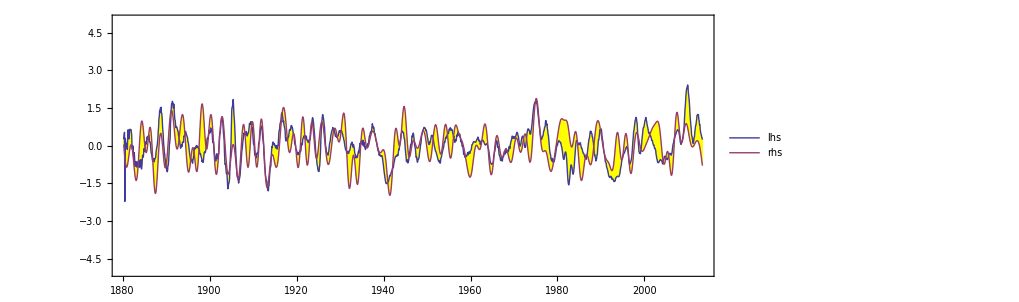

```mathematica
(*  BAAAA D   
WinLowFilter = 214;    WinHiFilter = 9;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,7];
R = MeanFilter[RR,5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  dilate[x_] := -0.1*Sin[0.098*x-1];
OSC := 9.08;    
Hill[x_] := -0.21*12*12*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]));
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.438*Cos[2*Pi/7.3*x+0.47];
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.011+0.0001*x );  
(*
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.02, y[TR]==+0.03}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, Osc[x]-0.123*qbo[x-0.6]+First[-0.48*y[1.0004*x+dilate[x]+0.66] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
*)
lhs=Table[{1880.0+x, -R[[x*12]] - (2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])*Hill[x-0.5] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.3*RHS[x+dilate[x]+0.42] + 0.7*Osc[x+0.26]-0.123*qbo[x+0.1]},{x,STRT/12,LNGTH/12+0, 1/12}];     

OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.4]
```

{char t,4.23901,-0.115039, Years from,1880.25,to,2013.33,CC,51.0596,51.0694,0.00973171}

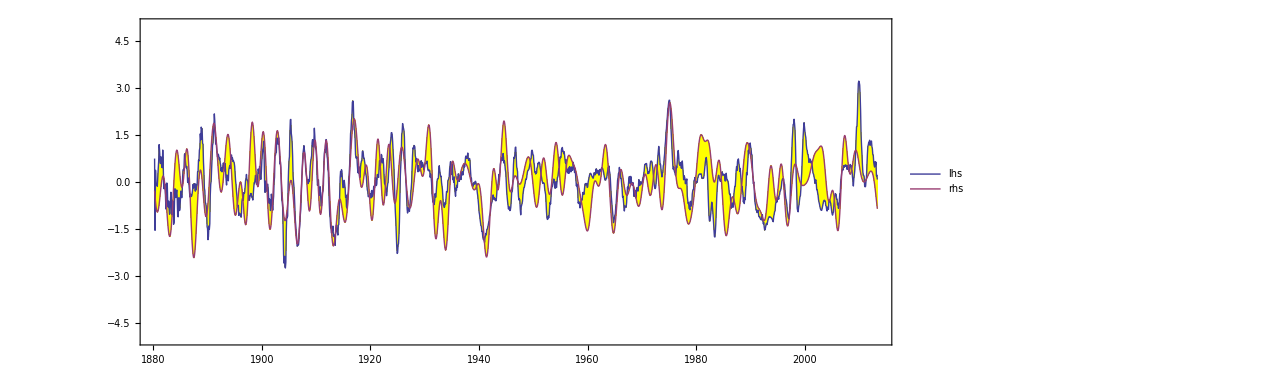

```mathematica
(* WinLowFilter = 210;    WinHiFilter = 7;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,5];
R = MeanFilter[RR,3];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  dilate[x_] := -0.14*Sin[0.093*x-0.8];
OSC := 9.07;    
Hill[x_] := -0.16*12*12*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]));
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.438*Cos[2*Pi/7.3*x+0.47];
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.011+0.0001*x );  
(* SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==-0.02, y[TR]==+0.03}, y, {x, 0, 260}];   
   SOIM=Table[{1880.0+x, Osc[x]-0.123*qbo[x-0.6]+First[-0.48*y[1.0004*x+dilate[x]+0.66] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     *)
lhs=Table[{1880.0+x, -R[[x*12]] - (2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])*Hill[x-0.17] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.4*RHS[x+dilate[x]+0.53] + 0.91*Osc[x+0.05]-0.3*qbo[x+0.25]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5},Frame->True,Axes->False, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.4]
```

{char t,4.23805,-0.0536067, Years from,1880.25,to,2013.33,CC,42.2755,42.2755,7.10543×10^-15}

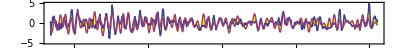

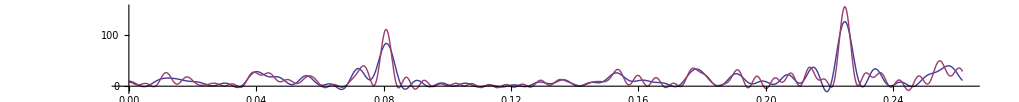

```mathematica
(* WinLowFilter = 210;    WinHiFilter = 7;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,5];
R = MeanFilter[RR,3];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.198;  dilate[x_] := -0.18*Sin[0.09*x-0.75];
Hill[x_] := -0.94*(12/2)*(12/2)*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]));
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.0001*x );  
lhs=Table[{1880.0+x, -R[[x*12]] - (2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])*Hill[x-0.4] },{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, -0.57*RHS[x+dilate[x]+0.47] },{x,STRT/12,LNGTH/12, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5},Frame->True,Axes->False, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.1] 

SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1]
```

{char t,4.23805,0.0517857, Years from,1880.25,to,2013.33,CC,49.5924,44.2942,-5.29828}

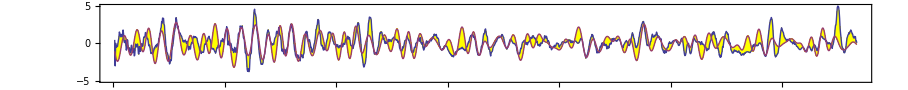

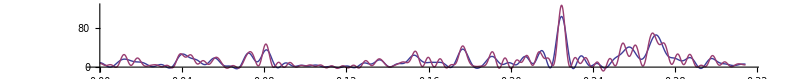

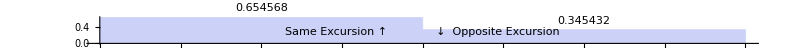

```mathematica
(* WinLowFilter = 210;    WinHiFilter = 7;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,5];
R = MeanFilter[RR,3];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.198;  dilate[x_] := -0.18*Sin[0.09*x-0.75];
Hill[x_] := -0.94*(12/2)*(12/2)*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]));
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.0001*x );  
lhs=Table[{1880.0+x, -R[[x*12]] - (2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])*Hill[x-0.4] },{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, 1.3*(-0.57*RHS[x+dilate[x]+0.47]-0.32*cw[x+0.4]-0.46*qbo[x+0.15] -0*0.39*Cos[2*Pi/2.332*x-0.55]) },{x,STRT/12,LNGTH/12, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5},Frame->True,Axes->False, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.1] 

SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,3.75492,0.36423, Years from,1880.25,to,2013.33,CC,52.6482,52.6737,0.0254719}

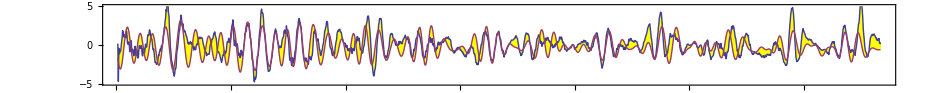

```mathematica
(* WinLowFilter = 210;    WinHiFilter = 7;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,5];
R = MeanFilter[RR,3];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.8;  dilate[x_] := -0.18*Sin[0.09*x-0.75];
Hill[x_] := -0.94*(12/2)*(12/2)*(CF+0.3*tsi[x+0]*(1.3+0.5*qbo[x+0.3]));
RHS[x_] := 2.98*(1.19*qbo[x+0.77]*(0.9+0.17*tsi[x-0.9])-0.18*cw[x+0.03]+0.05*tsi[x+3.9]+0.002*x );  
lhs=Table[{1880.0+x, -R[[x*12]] - (2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])*Hill[x-0.4] },{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, 1.3*(-0.54*RHS[x+dilate[x]+0.46]-0.22*cw[x+0.4]-0.7*qbo[x+0.15] -0*0.39*Cos[2*Pi/2.332*x-0.55]) },{x,STRT/12,LNGTH/12, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5},Frame->True,Axes->False, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.1]
```

{char t,3.75492,0.36423, Years from,1880.25,to,2013.33,CC,52.6737,52.6737,0.}

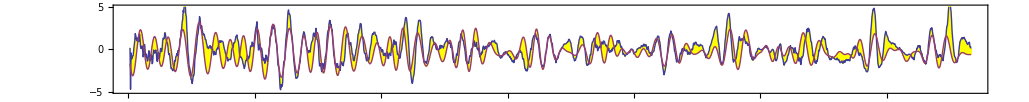

```mathematica
(* WinLowFilter = 210;    WinHiFilter = 7;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,5];
R = MeanFilter[RR,3];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.8;  dilate[x_] := -0.18*Sin[0.09*x-0.75];
Hill[x_] := -0.94*(12/2)*(12/2)*(CF+0.3*tsi[x+0]*(1.3+0.5*qbo[x+0.3]));
RHS[x_] := 2.98*(1.19*qbo[x+0.77]*(0.9+0.17*tsi[x-0.9])-0.18*cw[x+0.03]+0.05*tsi[x+3.9]+0.002*x );  
lhs=Table[{1880.0+x, -R[[x*12]] - (2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])*Hill[x-0.4] },{x,STRT/12,LNGTH/12, 1/12}];     
rhs=Table[{1880.0+x, 0*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])*Hill[x-0.4]+1.3*(-0.54*RHS[x+dilate[x]+0.46]-0.22*cw[x+0.4]-0.7*qbo[x+0.15] -0*0.39*Cos[2*Pi/2.332*x-0.55]) },
                  {x,STRT/12,LNGTH/12, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5},Frame->True,Axes->False, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.1]
```

{char t,4.23901,0.0184483, Years from,1880.25,to,2013.33,CC,36.6527,36.0352,-0.617486}

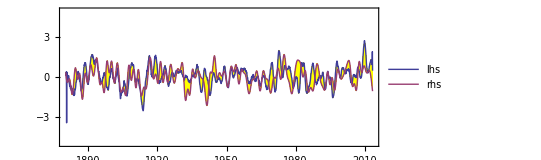

```mathematica
WinLowFilter = 214;    WinHiFilter = 11;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,9];
R = MeanFilter[RR,7];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  dilate[x_] := -0*0.1*Sin[0.098*x-1];
OSC := 9.08;    
Hill[x_] := -0.551*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]));
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.438*Cos[2*Pi/7.3*x+0.47];
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.011+0.0001*x );  
lhs=Table[{1880.0+x,  R[[x*12]]*Hill[x-0.35]+12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]]) },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0*R[[x*12]]*Hill[x-0.35]+0.5*(-0.36*RHS[x+dilate[x]+0.44] + 1.9*Osc[x+0.25])},{x,STRT/12,LNGTH/12+0, 1/12}];     

OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.4]
```

{char t,4.23901,0.00549332, Years from,1880.25,to,2013.33,CC,59.7247,59.7975,0.0727859}

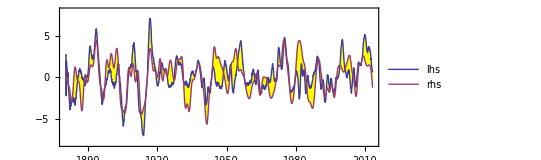

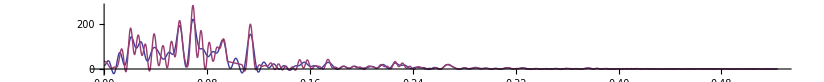

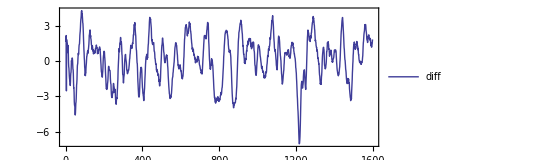

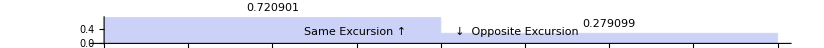

```mathematica
WinLowFilter = 210;    WinHiFilter = 9;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,7];
R = MeanFilter[RR,5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  dilate[x_] := -0*0.3*Sin[0.1*x-1];
OSC := 9.08;    
Hill[x_] := -1.45*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]));
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.39*Cos[2*Pi/7.34*x+0.47];
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.011+0.0001*x );  
lhs=Table[{1880.0+x,  R[[x*12]]*Hill[x-0.36]+12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]]) },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 1.9*(-0.2*RHS[x+dilate[x]+0.6]+0.6*Cos[2*Pi/4.5*x+1.3]+1.9*Osc[x+0.1] - 0.2*qbo[x+0.2])},{x,STRT/12,LNGTH/12+0, 1/12}];     

OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.4] 

SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/6},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},Frame->True,Axes->False, PlotLegends->{"diff"},AspectRatio->0.4] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,-0.0751135, Years from,1880.25,to,2013.33,CC,61.7459,61.198,-0.547852}

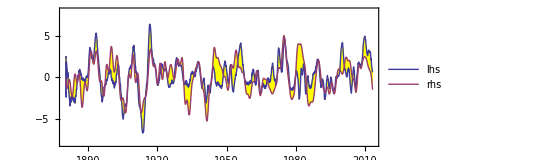

```mathematica
WinLowFilter = 210;    WinHiFilter = 9;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,7];
R = MeanFilter[RR,5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  dilate[x_] := -0*0.13*Sin[0.1*x-0.9];
OSC := 9.085;    
Hill[x_] := -1.36*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43]));
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.45]-0.3*Cos[4*Pi/OSC*x+2.18]) - 0.356*Cos[2*Pi*x/(3*OSC)-0.6] +0.39*Cos[2*Pi/7.34*x+0.47];
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]+0.0001*x );  
lhs=Table[{1880.0+x,  R[[x*12]]*Hill[x-0.26]+12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]]) },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 3.1*(-0.18*RHS[x+dilate[x]+0.62]+1.1*Osc[x+0.12]-0.26*qbo[x+0.26])},{x,STRT/12,LNGTH/12+0, 1/12}];     

OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.4]
```

{char t,4.23901,1.68285, Years from,1880.25,to,2013.33,CC,79.9707,79.9707,0.}

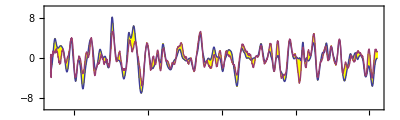

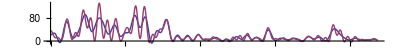

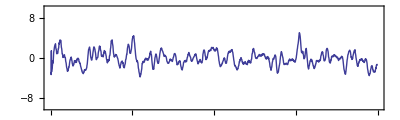

```mathematica
WinLowFilter = 210;    WinHiFilter = 9;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,7];
R = MeanFilter[RR,5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  dilate[x_] := -0.08*Sin[0.102*x-0.93];
OSC := 9.085;    
Hill[x_] := -1.25*(CF+0.357*tsi[x-1.55]*(1.03+0.62*qbo[x+0.43])) ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.5]-0.24*Cos[4*Pi/OSC*x+2.2]) - 0.26*Cos[2*Pi*x/(3*OSC)-0.5] +0.3*Cos[2*Pi/7.34*x+0.47];
RHS[x_] := 2.98*(0.8219*qbo[x+0.71]*(0.98+0.16*tsi[x+0.62])-0.438*cw[x+0.04]+0.0082*tsi[x+3.9]);  
lhs=Table[{1880.0+x,  -R[[x*12]]*Hill[x-0.26] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -(-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]]) +
                    3.1*(-0.178*RHS[x+dilate[x]+0.7]+0.69*Osc[x+0.08]-0.26*qbo[x+0.26])) },{x,STRT/12,LNGTH/12+0, 1/12}];     

OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 

SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3]
```

{char t,4.23901,0.0236259, Years from,1880.25,to,2013.33,CC,81.0018,83.9197,2.91785}

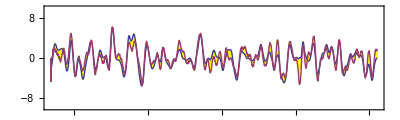

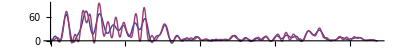

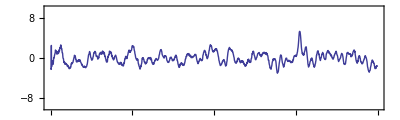

```mathematica
WinLowFilter = 210;    WinHiFilter = 9;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-1*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-1*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,7];
R = MeanFilter[RR,5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  
OSC := 9.087;    
Hill[x_] := -1.13*(CF+0.2*tsi[x-0.5]*(1.3+0.66*qbo[x+0.4])) ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.5]-0.24*Cos[4*Pi/OSC*x+2.2]) - 0.26*Cos[2*Pi*x/(3*OSC)-0.5] +0.32*Cos[2*Pi/7.34*x+0.47];
RHS[x_] := 2.98*(0.19*qbo[x+0.38]-0.441*cw[x+0.1]+0.06*tsi[x+3.2]);  
lhs=Table[{1880.0+x,  -R[[x*12]]*Hill[x-0.33] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -(-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+3.1*(-0.18*RHS[x+0.74]+0.67*Osc[x+0.09])) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 

SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3]
```

{char t,4.23901,0.093354, Years from,1880.25,to,2013.33,CC,85.1917,85.8874,0.6957}

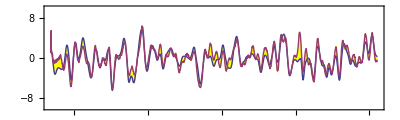

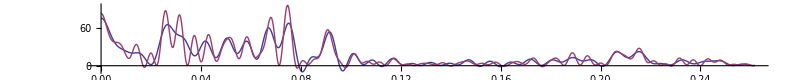

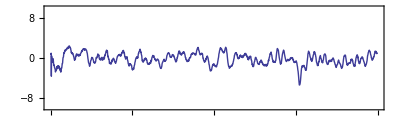

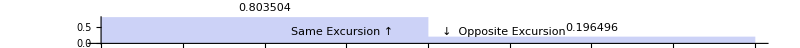

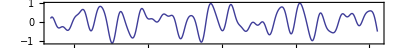

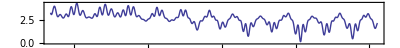

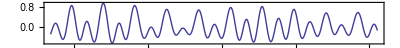

```mathematica
WinLowFilter = 205;    WinHiFilter = 9;  
RRR = (1*MeanFilter[darwin[[All,2]],WinHiFilter]-0*MeanFilter[darwin[[All,2]],WinLowFilter])-
      (1*MeanFilter[tahiti[[All,2]],WinHiFilter]-0*MeanFilter[tahiti[[All,2]],WinLowFilter]); 
RR = MeanFilter[RRR,7];
R = MeanFilter[RR,5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  
OSC := 9.087;    
Hill[x_] := 1.2*(CF+0.17*tsi[x-0.61]*(1.4+0.78*qbo[x+0.05])) ;
Osc[x_] := 0.534*(Cos[2*Pi/OSC*x+4.7]-0.24*Cos[4*Pi/OSC*x+2.2]) - 0.3*Cos[2*Pi*x/(3*OSC)-0.5] +0.32*Cos[2*Pi/7.34*x+0.47];
RHS[x_] := 2.98*(0.178*qbo[x+0.37]-0.44*cw[x+0.1]+0.07*tsi[x+3] +0.3*cw[x/2+1.25] );  
lhs=Table[{1880.0+x,  -Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+3.1*(-0.17*RHS[x+0.74]+0.67*Osc[x-0.0]) +0.7*Cos[2*Pi/47*x+0.9]) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 

SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]

osc = Table[{1880+i/12, Osc[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{osc}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"osc"}]
hill = Table[{1880+i/12, Hill[i/12]},{i,STRT,LNGTH,1}];
ListLinePlot[{hill}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"hill"}]
chandler = Table[{1880+i/12, -0.44*cw[i/12+0.1]+0.3*cw[i/12/2+1.25]},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"hill"}]
```

{char t,4.23901,0.093966, Years from,1880.25,to,2013.33,CC,82.7126,86.4539,3.74133}

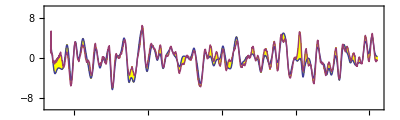

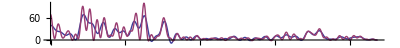

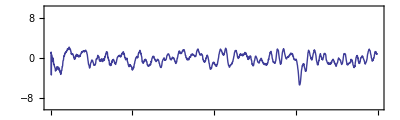

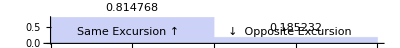

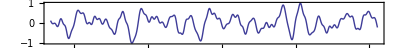

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),7],5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  
OSC := 9.087;    
Hill[x_] := 1.2*(CF+0.168*tsi[x-0.3]*(1.6+0.61*qbo[x+0.12])) ;
Osc[x_] := 0.5*(Cos[2*Pi/OSC*x+4.6]-0.24*Cos[4*Pi/OSC*x+2.3]) - 0.3*Cos[2*Pi*x/(3*OSC)-0.5] +0.32*Cos[2*Pi/7.33*x+0.47];
RHS[x_] := 2.98*(0.178*qbo[x+0.38]-0.48*cw[x+0.08] +0.29*cw[x/2+1.25] );  
lhs=Table[{1880.0+x,  -Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+3.2*(-0.17*RHS[x+0.74]+0.68*Osc[x-0.0]) +0.67*Cos[2*Pi/47*x+0.9]) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 

SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]

chandler = Table[{1880+i/12, (-0.17*RHS[i/12+0.74]+0.68*Osc[i/12-0.0])},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"forcing"}]
```

{char t,4.23901,0.65325, Years from,1880.25,to,2013.33,CC,78.2928,78.6117,0.318912}

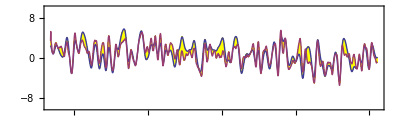

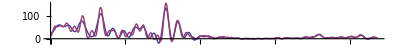

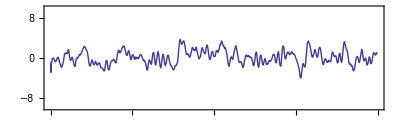

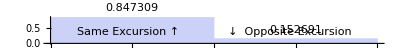

```mathematica
WinHiFilter = 7;  
R = MeanFilter[MeanFilter[MeanFilter[NINO34[[All,2]],WinHiFilter],5],3];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  
OSC := 9.087;    
Hill[x_] := 1.7*(CF+0*0.168*tsi[x-0.3]*(1.6+0.61*qbo[x+0.12])) ;
Osc[x_] := 0.5*(Cos[2*Pi/OSC*x+4.6]-0.24*Cos[4*Pi/OSC*x+2.3]) - 0.3*Cos[2*Pi*x/(3*OSC)-0.5] +0.32*Cos[2*Pi/7.33*x+0.47];
RHS[x_] := 2.98*(0.178*qbo[x+0.38]-0.48*cw[x+0.08] +0.29*cw[x/2+1.25] +0.018*x -1.8 );  
lhs=Table[{1880.0+x,  -Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+2.3*(-0.17*RHS[x+0.74]+0.68*Osc[x-0.0]) +0.67*Cos[2*Pi/47*x+0.9]) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.23901,-0.00330158, Years from,1880.25,to,2013.33,CC,82.0182,82.0182,0.}

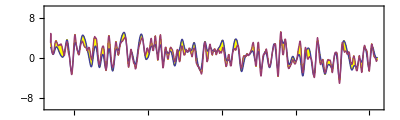

5.69129

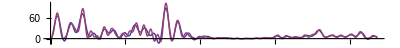

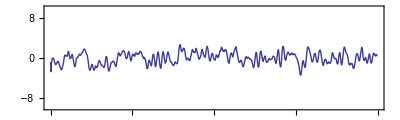

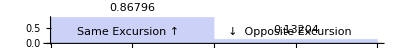

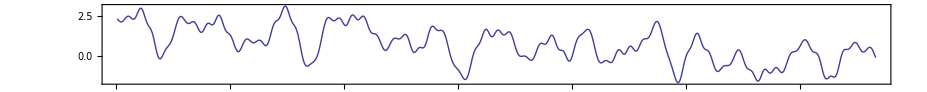

```mathematica
WinHiFilter = 7;  
R = MeanFilter[MeanFilter[MeanFilter[NINO34[[All,2]],WinHiFilter],5],3];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  
OSC := 9.087;    
Hill[x_] := 1.5*(CF+0*0.168*tsi[x-0.3]*(1.6+0.61*qbo[x+0.12])) ;
Osc[x_] := 0.5*(Cos[2*Pi/OSC*x+4.6]-0.24*Cos[4*Pi/OSC*x+2.3]) - 0.26*Cos[2*Pi*x/(3*OSC)-0.5] +0.2*Cos[2*Pi/7.33*x+0.47];
RHS[x_] := 2.98*(0.178*qbo[x+0.4]-0.48*cw[x+0.11] +0.6*cw[x/2+0.7] +0.016*x -1.7 );  
lhs=Table[{1880.0+x,  -Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+2.3*(-0.17*RHS[x+0.7]+0.5*Osc[x-0.0]) +0.3*Cos[2*Pi/47*x+0.9]) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.092/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/12},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]

chandler = Table[{1880+i/12, 2.3*(-0.17*RHS[i/12+0.7]+0.5*Osc[i/12-0.0]) +0.3*Cos[2*Pi/47*i/12+0.9]},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"chandler"}]
```

{char t,4.23901,-0.226176, Years from,1880.25,to,2013.33,CC,88.9883,88.9933,0.00503142}

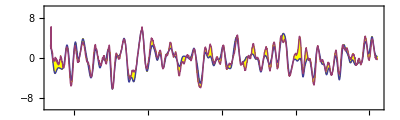

5.81776

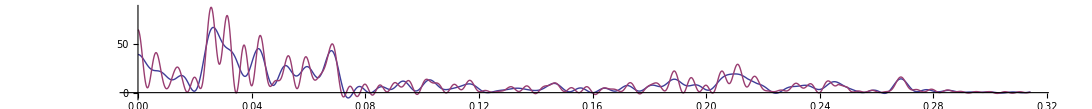

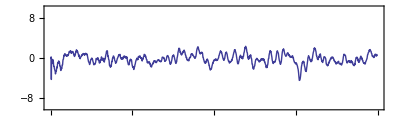

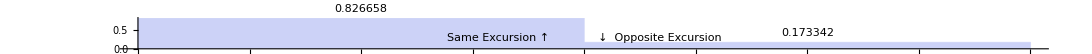

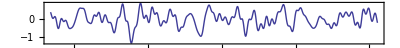

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),7],5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  
OSC := 9.087;    
Hill[x_] := 1.18*(CF+0.168*tsi[x-0.3]*(1.6+0.63*qbo[x+0.12])) ;
(* Hill[x_] := 0.85*(CF) ; *)
Osc[x_] := 0.5*(Cos[2*Pi/OSC*x+4.6]-0.24*Cos[4*Pi/OSC*x+2.3]) - 0.3*Cos[2*Pi*x/(3*OSC)-0.5] +0.32*Cos[2*Pi/7.33*x+0.47];
RHS[x_] := 2.98*(0.28*qbo[x+0.4]-0.48*cw[x+0.08] +0.29*cw[x/2+1.25] +0.23*Cos[2*Pi/2.45*x+1.1] + 0.3*Cos[2*Pi/7*x+2.2] + 0.3*Cos[2*Pi/5.8*x+1]);  
lhs=Table[{1880.0+x,  -Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+3.2*(-0.17*RHS[x+0.74]+0.68*Osc[x-0.0]) +0.67*Cos[2*Pi/47*x+0.9]) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.09/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]

chandler = Table[{1880+i/12, (-0.17*RHS[i/12+0.74]+0.68*Osc[i/12-0.0])},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"forcing"}]
```

{char t,4.23901,-0.0395518, Years from,1880.25,to,2013.33,CC,85.2968,89.3748,4.078}

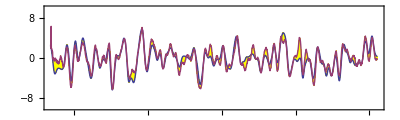

27.5578

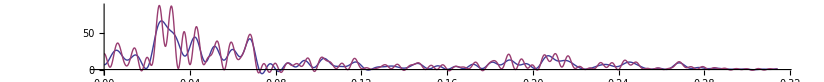

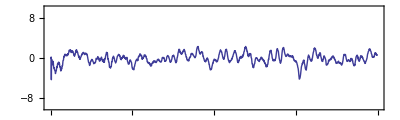

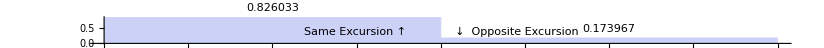

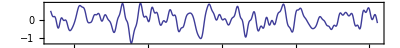

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),7],5];
STRT=3; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.197;  
OSC := 9.087;    HALEA := 10.6;
tsiA[x_] := -0.3*Cos[2*Pi/HALEA*x+3.1]+0.5*Cos[1*Pi/HALEA*x+4.1];
Hill[x_] := 1.22*(CF+0.167*tsi[x-0.3]*(1.6+0.7*qbo[x+0.2])) ;
(* Hill[x_] := 0.85*(CF) ; *)
Osc[x_] := 0.5*(Cos[2*Pi/OSC*x+4.6]-0.24*Cos[4*Pi/OSC*x+2.3]) - 0.3*Cos[2*Pi*x/(3*OSC)-0.5] +0.32*Cos[2*Pi/7.33*x+0.47];
RHS[x_] := 2.98*(0.19*qbo[x+0.38]-0.5*cw[x+0.08] +0.3*cw[x/2+1.25]-0.03*tsi[x-2.8] + 0.17*Cos[2*Pi/2.452*x+1.4]+ 0.3*Cos[2*Pi/7*x+2.2] + 0.3*Cos[2*Pi/5.82*x+1.29]);  
lhs=Table[{1880.0+x,  -Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+3.2*(-0.17*RHS[x+0.75]+0.68*Osc[x-0.1]) +0.68*Cos[2*Pi/47*x+0.9]-0.1) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.019/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]

chandler = Table[{1880+i/12, (-0.17*RHS[i/12+0.74]+0.68*Osc[i/12-0.0])},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"forcing"}]
```

{char t,4.23998,0.0505274, Years from,1881.,to,2013.33,CC,92.4903,93.842,1.35167}

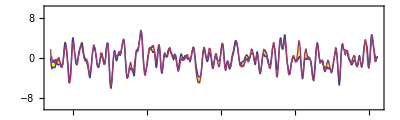

2.90888

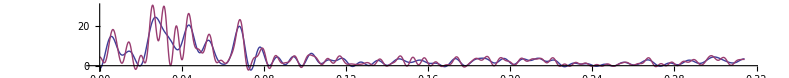

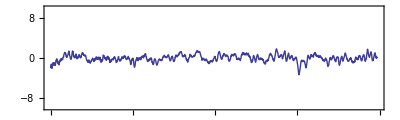

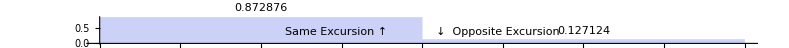

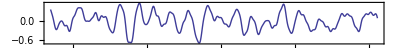

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),WinHiFilter-2],WinHiFilter-4];
WinHiFilter = 5;  
RR = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),WinHiFilter-2],WinHiFilter-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.196;  
OSC := 9.074;    
Hill[x_] := 0.79*(CF+0.18*tsi[x-0.28]) ;
(* Hill[x_] := 0.85*(CF) ; *)
Osc[x_] := 0.4*(Cos[2*Pi/OSC*x+4.6]-0.18*Cos[4*Pi/OSC*x+2.5]) - 0.18*Cos[2*Pi*x/(3*OSC)-0.55] +0.26*Cos[2*Pi/7.33*x+0.4] -0.156*Cos[2*Pi/8.85*x+3.4];
RHS[x_] := 2.98*(0.17*qbo[x-1.1]-0.37*cw[x+0.12] +0.19*cw[x/2+1.2]-0.04*tsi[x-2.7]+0.16*Cos[2*Pi/2.327*x+1.1]+ 0.26*Cos[2*Pi/7*x+2.2]-0.09*Cos[2*Pi/2.91*x+0.4] + 0.14*Cos[2*Pi/5.82*x+1.4]);  
lhs=Table[{1880.0+x,  -Hill[x]*RR[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+3.2*(-0.17*RHS[x+0.75]+0.68*Osc[x-0.1]) +0.44*Cos[2*Pi/47*x+0.9]-0.1) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.18/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]

chandler = Table[{1880+i/12, (-0.17*RHS[i/12+0.75]+0.68*Osc[i/12-0.1])},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"forcing"}]
```

{char t,4.23998,-2.85985, Years from,1881.,to,2013.33,CC,84.2524,84.2664,0.0140175}

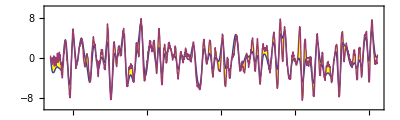

2.43534

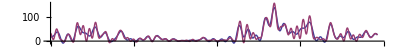

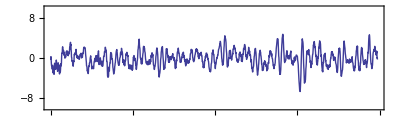

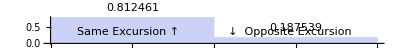

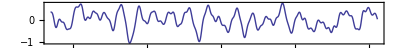

```mathematica
WinHiFilter = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),WinHiFilter-2],WinHiFilter-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.196;  
OSC := 9.075;    
Hill[x_] := 1.2*(CF+0.18*tsi[x-0.26]) ;
(* Hill[x_] := 0.85*(CF) ; *)
Osc[x_] := 0.5*(Cos[2*Pi/OSC*x+4.6]-0.18*Cos[4*Pi/OSC*x+2.5]+0.32*Cos[Pi/(2*OSC)*x+3.2]) - 0.18*Cos[2*Pi*x/(3*OSC)-0.55] +0.26*Cos[2*Pi/7.33*x+0.4] -0.13*Cos[2*Pi/8.85*x+3.4];
RHS[x_] := 2.98*(0.15*qbo[x-1.5]-0.5*cw[x+0.11] +0.31*cw[x/2+1.2]-0.07*tsi[x-2.6]+0.12*Cos[2*Pi/2.327*x+1.3]+ 0.28*Cos[2*Pi/7*x+2.2]-0.13*Cos[2*Pi/2.91*x+0.4] + 0.23*Cos[2*Pi/5.82*x+1.4]);  
lhs=Table[{1880.0+x,  -Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, (-12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])+3.2*(-0.17*RHS[x+0.75]+0.68*Osc[x-0.1]) +0.67*Cos[2*Pi/47*x+0.9]-0.1) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.215/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-10,10},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]

chandler = Table[{1880+i/12, (-0.17*RHS[i/12+0.75]+0.68*Osc[i/12-0.1])},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"forcing"}]
```

{char t,5.1302,-0.0522526, Years from,1881.,to,2013.33,CC,66.4156,71.0612,4.64554}

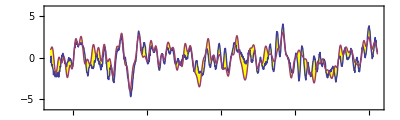

1.925

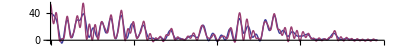

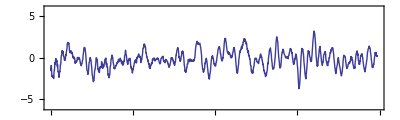

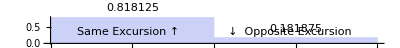

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),WinHiFilter-2],WinHiFilter-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 1.5;  
OSC := 9.075;    
Hill[x_] := 1.46*(CF-0*0.1*cw[x-0.2]+0.21*tsi[x-0.4]*(1-0.3*qbo[x-1.])) ;
(* Hill[x_] := 0.85*(CF) ; *)
Osc[x_] := 0.5*(Cos[2*Pi/OSC*x+4.6]-0.19*Cos[4*Pi/OSC*x+2.5]+0.34*Cos[Pi/(2*OSC)*x+3.2]) - 0.17*Cos[2*Pi*x/(3*OSC)-0.55] +0.26*Cos[2*Pi/7.33*x+0.4] -0.13*Cos[2*Pi/8.85*x+3.4];
RHS[x_] := 2.98*(0.075*qbo[x-1.9]*(1+0.8*tsi[x-2])-0.55*cw[x+0.12]+0.28*cw[x/2+1.3]-0.07*tsi[x-2.6]+0.29*Cos[2*Pi/2.327*x+1.9]+0.4*Cos[2*Pi/7*x+2.5]+
             0.008*Cos[2*Pi/2.46*x-0.3]-0.02*Cos[2*Pi/2.9*x-0.5]+0.32*Cos[2*Pi/5.82*x+1.4]);  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 0.57*(+7.4*(-0.123*RHS[x+0.8]+0.6*Osc[x-0.1]) +0.7*Cos[2*Pi/47*x+1.1]-0.0) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.272/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,800,1200,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.57034,-0.00611969, Years from,1881.,to,1980.,CC,71.2037,86.6326,15.4288}

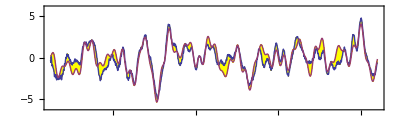

1.925

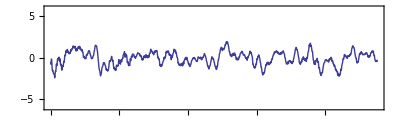

-Graphics-

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),WinHiFilter-2],WinHiFilter-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
CF = 1.89;   QBW=2.328;
OSC := 9.09;    
Hill[x_] := 1.47*(CF+0.14*tsi[x-0.4]*(1-0.2*qbo[x-1.])) ;
(* Hill[x_] := 0.85*(CF) ; *)
Osc[x_] := 0.49*(1.0*Cos[2*Pi/OSC*x+4.58]-0.08*Cos[4*Pi/OSC*x+2.5]+0.2*Cos[Pi/(2*OSC)*x+3.8]) - 0.23*Cos[2*Pi*x/(3*OSC)-0.55] +0.32*Cos[2*Pi/7.33*x+0.4] -0.15*Cos[2*Pi/8.85*x+3.2];
RHS[x_] := 2.98*(0.0*qbo[x-0.8]*(1+0.8*tsi[x-2])-0.57*cw[x+0.12]+0.27*cw[x/2+1.58]+0.07*tsi[x-2.3]+0.38*Cos[2*Pi/QBW*x+2.3]+0.38*Cos[2*Pi/(QBW*3)*x+2.3]+
             0.00*Cos[2*Pi/2.46*x-0.3]-0.24*Cos[2*Pi/2.9*x-0.5]+0.32*Cos[2*Pi/5.821*x+1.3]);  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 0.7*(+7.5*(-0.098*RHS[x+0.74]+0.58*Osc[x-0.21]) +0.68*Cos[2*Pi/47*x+1.1]-0.0) },
            {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.272/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),WinHiFilter-2],WinHiFilter-4];
STRT=12; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
CF = 1.89;   QBW=2.326;   OSC := 9.09;    
Hill[x_] := 1.47*(CF+0.12*tsi[x]) ;
Osc[x_] := 0.49*(1.0*Cos[2*Pi/OSC*x+4.58]-0.08*Cos[4*Pi/OSC*x+2.5]+0.2*Cos[Pi/(2*OSC)*x+3.8])-0.23*Cos[2*Pi*x/(3*OSC)-0.55]+0.32*Cos[2*Pi/7.33*x+0.4] -
           0.15*Cos[2*Pi/8.848*x+3.2];
RHS[x_] := 2.98*(-0.42*Cos[2*Pi/21*x+2.5]-0.57*cw[x+0.12]+0.27*cw[x/2+1.58]+0.071*tsi[x-2.3]+0.38*Cos[2*Pi/QBW*x+2.3]+0.38*Cos[2*Pi/(QBW*3)*x+2.3]+
             -0.24*Cos[2*Pi/2.91*x-0.5]+0.32*Cos[2*Pi/5.821*x+1.3]);  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 0.67*(+7.5*(-0.098*RHS[x+0.74]+0.58*Osc[x-0.21]) +0.66*Cos[2*Pi/47*x+1.1]-0.0) }, {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.068/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.57034,-0.0335772, Years from,1881.,to,1980.,CC,90.5372,90.5379,0.000729505}

-Graphics-

7.69998

-Graphics-

-Graphics-

-Graphics-

```mathematica
Window = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=11; STRTY=1880+STRT/12;LNGTH=1200; ENDY=1880+LNGTH/12; 
CF = 2.89;   QBW=2.327;   OSC = 9.09;    TSP = 21.97;
dilate[x_] := -0.13*Sin[0.074*x+0.0];
TSI[x_] := -0.42*Cos[2*Pi/TSP*x+3.5]+0.071*tsi[x-2.3] -0.67*Cos[2*Pi/(TSP/3)*x-0.43];
Hill[x_] := CF+0.17*tsi[x] ;
Tide9[x_] := 0.5*(1.0*Cos[2*Pi/OSC*x+4.58]-0.14*Cos[4*Pi/OSC*x+2.7]+0.21*Cos[Pi/(2*OSC)*x+3.7])-0.26*Cos[2*Pi*x/(3*OSC)-0.3];
Osc[x_] := Tide9[x] - 0.15*Cos[2*Pi/8.848*x+3.2] -0.13*Cos[2*Pi/8*x+5.2] ;
qbw[x_] := 0.38*Cos[2*Pi/QBW*x+2.3]+0.38*Cos[2*Pi/(QBW*3)*x+2.3]-0.24*Cos[2*Pi/2.91*x-0.5];
cwb[x_] := -0.57*cw[x+0.12]+0.3*cw[x/2+1.58]+0.32*Cos[2*Pi/5.82*x+1.4];
RHS[x_] := 2.9*qbw[x+0.02]+2.98*TSI[x-0.08]+2.9*cwb[x-0.11] -5.92*Osc[x-0.81]-0.94*Cos[2*Pi/48*x+1.1];  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 0.69*(-0.73*RHS[x+dilate[x]+0.74] -0.0) }, {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.0655/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
chandler = Table[{1880+i/12, (Osc[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (TSI[i/12])},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler,tsiw}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"cw","tsi"}]
```

{char t,3.69599,-0.0369241, Years from,1880.92,to,1980.,CC,91.5579,92.9863,1.42839}

-Graphics-

7.99387

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
Window = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=11; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -1.1*R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.89;   QBW=2.327;   OSC = 9.09;    TSP = 21.97;
dilate[x_] := -0.13*Sin[0.074*x+0.0];
TSI[x_] := -0.42*Cos[2*Pi/TSP*x+3.5]+0.071*tsi[x-2.3] -0.67*Cos[2*Pi/(TSP/3)*x-0.43];
Hill[x_] := CF+0.17*tsi[x] ;
Tide9[x_] := 0.5*(1.0*Cos[2*Pi/OSC*x+4.58]-0.14*Cos[4*Pi/OSC*x+2.7]+0.21*Cos[Pi/(2*OSC)*x+3.7])-0.26*Cos[2*Pi*x/(3*OSC)-0.3];
Osc[x_] := Tide9[x] - 0.15*Cos[2*Pi/8.848*x+3.2] -0.13*Cos[2*Pi/8*x+5.2] ;
qbw[x_] := 0.38*Cos[2*Pi/QBW*x+2.3]+0.38*Cos[2*Pi/(QBW*3)*x+2.3]-0.24*Cos[2*Pi/2.91*x-0.5];
cwb[x_] := -0.57*cw[x+0.12]+0.3*cw[x/2+1.58]+0.32*Cos[2*Pi/5.82*x+1.4];
RHS[x_] := 2.9*qbw[x+0.02]+2.98*TSI[x-0.08]+2.9*cwb[x-0.11] -5.92*Osc[x-0.81]-0.94*Cos[2*Pi/48*x+1.1];  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 0.69*(-0.73*RHS[x+0*dilate[x]+0.74] -0.0) }, {x,STRT/12,LNGTH/12+0, 1/12}];     
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.08],  y'[TR]==1.7, y[TR]==-0.21}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, +First[-0.48*y[1.0*x+0.8] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, PlotRange->{-3,3}, Frame->True, Axes->True, PlotLegends->{"SOI-Model"}, AspectRatio->0.2]
```

{char t,3.69599,-0.311289, Years from,1880.92,to,2013.33,CC,60.0964,35.7362,-24.3602}

-Graphics-

-Graphics-

```mathematica
Window = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=1200; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 2.89;   QBW=2.327;   OSC = 9.09;    TSP = 21.97;
dilate[x_] := -0.13*Sin[0.074*x+0.0];
TSI[x_] := -0.42*Cos[2*Pi/TSP*x+3.5]+0.071*tsi[x-2.3] -0.67*Cos[2*Pi/(TSP/3)*x-0.43];
Hill[x_] := CF+0.2*tsi[x] ;
Tide9[x_] := 0.5*(1.0*Cos[2*Pi/OSC*x+4.58]-0.14*Cos[4*Pi/OSC*x+2.7]+0.21*Cos[Pi/(2*OSC)*x+3.7])-0.26*Cos[2*Pi*x/(3*OSC)-0.3];
Osc[x_] := Tide9[x] - 0.15*Cos[2*Pi/8.848*x+3.2] -0.13*Cos[2*Pi/8*x+5.2] ;
qbw[x_] := 0.38*Cos[2*Pi/QBW*x+2.3]+0.38*Cos[2*Pi/(QBW*3)*x+2.3]-0.24*Cos[2*Pi/2.91*x-0.5];
cwb[x_] := -0.57*cw[x+0.12]+0.3*cw[x/2+1.58]+0.32*Cos[2*Pi/5.82*x+1.4];
RHS[x_] := 2.9*qbw[x-0.5]+2.98*TSI[x+1.9]+2.9*cwb[x-0.5] -5.92*Osc[x-1.81]-0.94*Cos[2*Pi/48*x+1.1];  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 0.8*(-0.73*RHS[x+dilate[x]+2.2] -0.0) }, {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.048/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
chandler = Table[{1880+i/12, (Osc[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (TSI[i/12])},{i,STRT,LNGTH,1}];
ListLinePlot[{chandler,tsiw}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"cw","tsi"}]
```

{char t,3.69599,0.200474, Years from,1980.,to,2013.33,CC,42.38,47.5665,5.18649}

-Graphics-

10.9083

-Graphics-

-Graphics-

-Graphics-

```mathematica
WinHiFilter = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]),WinHiFilter-2],WinHiFilter-4];
STRT=1200; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
CF = 1.92;  
OSC := 9.076;    
Hill[x_] := 1.48*(CF+0.21*tsi[x-0.4]) ;
Tide9[x_] := 0.45*(Cos[2*Pi/OSC*x+4.6]-0.1*Cos[4*Pi/OSC*x+2.5]+0.34*Cos[Pi/(2*OSC)*x+3.2])-0.1*Cos[2*Pi*x/(3*OSC)-0.55];
Osc[x_] := Tide9[x]+0.2*Cos[2*Pi/7.33*x+0.4]-0.1*Cos[2*Pi/8.85*x+3.4];
qbw[x_] := (0.13*qbo[x-1.5]*(1+0.9*tsi[x-1.5])+0.2*Cos[2*Pi/2.327*x+1.7]+0.2*Cos[2*Pi/7*x+2.0] -0.7*Cos[2*Pi/2.4589*x-0.89]);
cwb[x_] := -0.6*cw[x+0.12]+0.42*cw[x/2+1.3];
RHS[x_] := 2.98*(qbw[x]+cwb[x]-0.29*tsi[x-3.]);  
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, 0.68*(+6.*(-0.1*RHS[x+0.77]+0.5*Osc[x-0.69]) +1.4*Cos[2*Pi/47*x+0.9]) },  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
2*Pi/0.272/12
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 

SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.5345,-0.0523903, Years from,1980.,to,2013.33,CC,96.4942,94.2457,-2.24853}

-Graphics-

1.925

-Graphics-

-Graphics-

```mathematica
(* cwb[x_] := -0.55*Cos[2*Pi*x/CWP+0.3]-0.31*Cos[2*Pi*x/2/CWP-1.3] + 0.4*Cos[2*Pi/5.8*x+1.4];
cwb[x_] := -0.61*cw[x+0.13]-0.32*Cos[2*Pi*x/2/CWP-1.2] + 0.26*Cos[2*Pi/5.8*x+1.5]; *)
dilate[x_] := -0.0*Sin[0.078*x+0.1];
Window = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=9; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;   TSP = 21.97;  TR1 = 99.4; TR = 99.4;  CF = 2.9;  OSC := 9.08;  CWP := 6.47;  
TSI[x_] := Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.87, 0.6] - 0.35*Cos[2*Pi/TSP*x+0.2] +
           If[x<TR, 0*0.5*Cos[2*Pi/17*x-0.2] + 0.2*tsi[x-2]-1.3*Cos[2*Pi/TSP*x+3.3],   -0.92*tsi[x-2.6]];
Hill[x_] := CF+0.25*tsi[x+0.48]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.57]-0.12*Cos[4*Pi/OSC*x+2.9]+0.19*Cos[Pi/(2*OSC)*x+3.5])-0.25*Cos[2*Pi*x/(3*OSC)-0.5];
Osc[x_] := 1.08*Tide9[x-0.01]-0.22*Cos[2*Pi/8.85*x+3] -0.11*Cos[2*Pi/8*x+5.5] +0.06*Cos[2*Pi/5*x+0.7] ;
qbw[x_] := +0.42*Cos[2*Pi/(QBW*3)*x+2.2]+0.22*Cos[2*Pi/QBW*x+2.5] -0*0.09*Cos[2*Pi/2.119*x-0.3] + 
                                     If[x<TR,-0.21*Cos[2*Pi/2.91*x-0.4],  -0.53*Cos[2*Pi/2.458*x-0.96]];
cwb[x_] := -0.6*cw[x+0.12]+0.28*cw[x/2+1.4] + 0.3*Cos[2*Pi/5.8*x+1.4];  
RHS[x_] := 3.0*qbw[x-0.01]+2.89*cwb[x-0.23]-1.18*Cos[2*Pi/48*x+1]-5.9*Osc[x-1.2] + 1.1*TSI[x] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.08*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.55*RHS[x+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
qbww = Table[{1880+i/12, (3*qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.017*TSI[i/12+3])},{i,STRT,LNGTH,1}];
ListLinePlot[{TSIT,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"qbw","tsi"}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.1/12
ListLinePlot[{SDIF},PlotRange->{-6,6},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,3.68961,0.0387705, Years from,1880.75,to,2013.33,CC,80.292,93.5089,13.2169}

-Graphics-

-Graphics-

-Graphics-

5.23599

-Graphics-

-Graphics-

```mathematica
Window = 9;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=11; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.331;   TSP = 21.97;  TR1 = 99.4; TR = 99.4;  CF = 2.81;  OSC := 9.08;    
TSI[x_] := Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.87, 0.6] + If[x<TR, 0.213*tsi[x-2.3]-1.25*Cos[2*Pi/TSP*x+3.5], -0.864*tsi[x-3.]];
Hill[x_] := CF+0.28*tsi[x+0.5]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.58]-0.14*Cos[4*Pi/OSC*x+2.6]+0.23*Cos[Pi/(2*OSC)*x+3.7])-0.24*Cos[2*Pi*x/(3*OSC)-0.5];
Osc[x_] := 1.06*Tide9[x]-0.18*Cos[2*Pi/8.85*x+3.1] -0.12*Cos[2*Pi/8*x+5.5] +0.06*Cos[2*Pi/5*x+0.6]  ;
qbw[x_] := +0.43*Cos[2*Pi/(QBW*3)*x+2.2]+0.46*Cos[2*Pi/QBW*x+2.5] + If[x<TR, -0*0.22*Cos[2*Pi/2.91*x-0.4],
                                                                               -0.5*Cos[2*Pi/2.458*x-0.89]];
cwb[x_] := -0.6*cw[x+0.12]+0.32*cw[x/2+1.5] + 0.26*Cos[2*Pi/5.8*x+1.5];
RHS[x_] := 4.4*qbw[x]*(1-0.1*Cos[2*Pi/TSP*x+2.1])/2+2.9*cwb[x-0.2]-1*Cos[2*Pi/48*x+1.1]-5.7*Osc[x-1.1] + TSI[x] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.08*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.56*RHS[x+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-6,6},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
qbww = Table[{1880+i/12, (3*qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.02*TSI[i/12+3])},{i,STRT,LNGTH,1}];
ListLinePlot[{TSIT,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"qbw","tsi"}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.02/12
```

{char t,3.74823,-0.0116298, Years from,1880.92,to,2013.33,CC,90.9096,90.9182,0.00859368}

-Graphics-

-Graphics-

-Graphics-

26.1799

```mathematica
(* cwb[x_] := -0.55*Cos[2*Pi*x/CWP+0.3]-0.31*Cos[2*Pi*x/2/CWP-1.3] + 0.4*Cos[2*Pi/5.8*x+1.4];
cwb[x_] := -0.61*cw[x+0.13]-0.32*Cos[2*Pi*x/2/CWP-1.2] + 0.26*Cos[2*Pi/5.8*x+1.5]; *)
dilate[x_] := -0.12*Sin[0.076*x-0.5] - 0.11*Sin[2*Pi*x+0.6];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333;   TSP = 21.89;  TR = 99.3;  CF = 3.71;  OSC := 9.091;  
TSI[x_] := 0.92*Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.8, 0.91] - 0.35*Cos[2*Pi/TSP*x+0.2] +
           If[x<TR, +0.18*tsi[x-2]-1.5*Cos[2*Pi/TSP*x+3.3],  -0.94*tsi[x-2.6]];
Hill[x_] := CF+0.28*tsi[x+0.48]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.57]-0.12*Cos[4*Pi/OSC*x+2.9]+0.19*Cos[Pi/(2*OSC)*x+3.5])-0.25*Cos[2*Pi*x/(3*OSC)-0.5];
Osc[x_] := 1.08*Tide9[x-0.01]-0.22*Cos[2*Pi/8.85*x+3] -0.11*Cos[2*Pi/8*x+5.5] +0.11*Cos[2*Pi/5*x+0.7] ;
qbw[x_] := +0.38*Cos[2*Pi/(QBW*3)*x+2.15]+0.23*Cos[2*Pi/QBW*x+2.7] -0.12*Cos[2*Pi/2.119*x-0.32] + 
                                     If[x<TR,-0.1*Cos[2*Pi/2.91*x-0.39],  -0.52*Cos[2*Pi/2.458*x-0.88]];
cwb[x_] := -0.6*cw[x+0.2]+0.28*cw[x/2+1.4] + 0.32*Cos[2*Pi/5.79*x+1.5];  
RHS[x_] := 1*3.55*qbw[x-0.01]+1*3.0*cwb[x-0.23]-1*1*Cos[2*Pi/48*x+1]-1*5.6*Osc[x-1.2] + 1*1.1*TSI[x] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.1*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.84*RHS[x+dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.3] 
qbww = Table[{1880+i/12, (3*qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.017*(TSI[i/12+3]))},{i,STRT,LNGTH,1}];
cwbb = Table[{1880+i/12, (0.0017*(1.5+cwb[i/12+1]))},{i,STRT,LNGTH,1}];
ListLinePlot[{CW,cwbb},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"cw","tsi"}]
ListLinePlot[{TSIT,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"tsi","model"}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/5},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.1/12
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.3] 
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,3.26207,0.0357286, Years from,1880.5,to,2013.33,CC,77.1286,89.006,11.8774}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

5.23599

-Graphics-

-Graphics-

```mathematica
(* cwb[x_] := -0.55*Cos[2*Pi*x/CWP+0.3]-0.31*Cos[2*Pi*x/2/CWP-1.3] + 0.4*Cos[2*Pi/5.8*x+1.4];
cwb[x_] := -0.61*cw[x+0.13]-0.32*Cos[2*Pi*x/2/CWP-1.2] + 0.26*Cos[2*Pi/5.8*x+1.5]; *)
dilate[x_] := -0.15*Sin[0.076*x-0.45] - 0.13*Sin[2*Pi*x+0.6];
Window = 7;  
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333;   TSP = 21.91;  TR = 99.3;  CF = 3.08;  OSC := 9.091;  
TSI[x_] := 0.85*Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.8, 1.0] - 0.75*Cos[2*Pi/TSP*x+0.3] +
           If[x<TR, +0.18*tsi[x-1.8]-1.8*Cos[2*Pi/TSP*x+3.3],  -0.94*tsi[x-2.5]];
Hill[x_] := CF+0.23*tsi[x+0.5]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.6]-0.09*Cos[4*Pi/OSC*x+3]+0.18*Cos[Pi/(2*OSC)*x+3.7])-0.24*Cos[2*Pi*x/(3*OSC)-0.4];
Osc[x_] := 1.1*Tide9[x]-0.24*Cos[2*Pi/8.85*x+3] -0.1*Cos[2*Pi/8*x+5.5] +0.07*Cos[2*Pi/5*x+0.7] ;
qbw[x_] := +0.42*Cos[2*Pi/(QBW*3)*x+2.25]+0.45*Cos[2*Pi/QBW*x+2.6] -0.24*Cos[2*Pi/2.119*x-0.33]  +
                                     If[x<TR,-0.265*Cos[2*Pi/2.91*x-0.48],  -1*Cos[2*Pi/2.458*x-0.8]];
cwb[x_] := -0.48*cw[x+0.22]+0.23*cw[x/2+1.5] + 0.28*Cos[2*Pi/5.79*x+1.4];  
RHS[x_] := 1*3.0*qbw[x]+1*3.2*cwb[x-0.23]-1*0.97*Cos[2*Pi/48*x+1]-1*5.4*Osc[x-1.2] + 1*1.11*TSI[x-0.02] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.11*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.72*RHS[x+dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.1/12
(*qbww = Table[{1880+i/12, (3*qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.017*(TSI[i/12+3]))},{i,STRT,LNGTH,1}];
cwbb = Table[{1880+i/12, (0.0017*(1.5+cwb[i/12+1]))},{i,STRT,LNGTH,1}];
ListLinePlot[{CW,cwbb},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"cw","tsi"}]
ListLinePlot[{TSIT,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"tsi","model"}]
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,3.58018,0.0649639, Years from,1880.5,to,2013.33,CC,83.9779,89.0767,5.09884}

-Graphics-

-Graphics-

-Graphics-

5.23599

```mathematica
(* This is original charcteristic frequency *)
(* cwb[x_] := -0.55*Cos[2*Pi*x/CWP+0.3]-0.31*Cos[2*Pi*x/2/CWP-1.3] + 0.4*Cos[2*Pi/5.8*x+1.4];
cwb[x_] := -0.61*cw[x+0.13]-0.32*Cos[2*Pi*x/2/CWP-1.2] + 0.26*Cos[2*Pi/5.8*x+1.5]; *)
dilate[x_] := -0.11*Sin[0.076*x-0.5] - 0.14*Sin[2*Pi*x+0.6];
Window = 7;  SEP=0;
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
STRT=6; STRTY=1880+STRT/12;LNGTH=1600; ENDY=1880+LNGTH/12; 
QBW=2.333;   TSP = 21.91;  TR = 99.3;  CF = 2.19;  OSC := 9.091;  
TSI[x_] := 0.83*Cos[2*Pi/(TSP/3)*x+2.5] * If[x<TR, 1.8, 1.0] - 0.65*Cos[2*Pi/TSP*x+0.2] +
           If[x<TR, +0.19*tsi[x-2]-1.7*Cos[2*Pi/TSP*x+3.3],  -0.97*tsi[x-2.6]];
Hill[x_] := CF+0.2*tsi[x+0.51]; 
Tide9[x_] := 0.44*(Cos[2*Pi/OSC*x+4.6]-0.09*Cos[4*Pi/OSC*x+2.9]+0.19*Cos[Pi/(2*OSC)*x+3.5])-0.25*Cos[2*Pi*x/(3*OSC)-0.5];
Osc[x_] := 1.1*Tide9[x-0.01]-0.24*Cos[2*Pi/8.85*x+3] -0.09*Cos[2*Pi/8*x+5.5] +0.03*Cos[2*Pi/5*x+0.7] ;
qbw[x_] := +0.32*Cos[2*Pi/(QBW*3)*x+2.15]+0.55*Cos[2*Pi/QBW*x+2.6] -0.22*Cos[2*Pi/2.119*x-0.32] + 
                                     If[x<TR,-0.26*Cos[2*Pi/2.91*x-0.45],  -1.18*Cos[2*Pi/2.458*x-0.88]];
cwb[x_] := -0.49*cw[x+0.21]+0.22*cw[x/2+1.4] + 0.27*Cos[2*Pi/5.79*x+1.5];  
RHS[x_] := 1*3.8*qbw[x]+1*3.1*cwb[x-0.23]-1*0.4*Cos[2*Pi/48*x+1]-1*5.48*Osc[x-1.2] + 1*1.12*TSI[x-0.01] ;  

lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]] - 0.1*(R[[x*12]])^3},{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, SEP-0.56*RHS[x+dilate[x]+0.8]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-8-SEP,8+SEP},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"lhs","rhs"},AspectRatio->0.2] 
SDIF = lhs[[All,2]]-rhs[[All,2]];  
ListLinePlot[{SDIF},PlotRange->{-8,8},Frame->True,Axes->True, PlotLegends->{"diff"},AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,800,400}],{ω,0,π/10},PlotRange->All,AspectRatio->0.1] 
qbww = Table[{1880+i/12, (3*qbw[i/12])},{i,STRT,LNGTH,1}];
tsiw = Table[{1880+i/12, (0.017*(TSI[i/12+3]))},{i,STRT,LNGTH,1}];
cwbb = Table[{1880+i/12, (0.0017*(1.5+cwb[i/12+1]))},{i,STRT,LNGTH,1}];
ListLinePlot[{CW,cwbb},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"cw","tsi"}]
ListLinePlot[{TSIT,tsiw},  AspectRatio->0.3, Frame->True, Axes->False, PlotLegends->{"tsi","model"}]
2*Pi/0.11/12
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,4.24578,-0.0362416, Years from,1880.5,to,2013.33,CC,83.9779,83.9779,0.}

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

4.75999

-Graphics-